```mathematica
Clear["Global`*"]
r[r_] := μ*r - r^3;
θ[r_] := ω + ν*r^2;
s = Solve[r[r] == 0, {r}]
velocity = Sqrt[μ]*θ[Sqrt[μ]];
length = 2*π*Sqrt[μ];
periodTime = length/velocity
```

{{r→0},{r→-√μ},{r→√μ}}

(2 π)/(μ ν+ω)

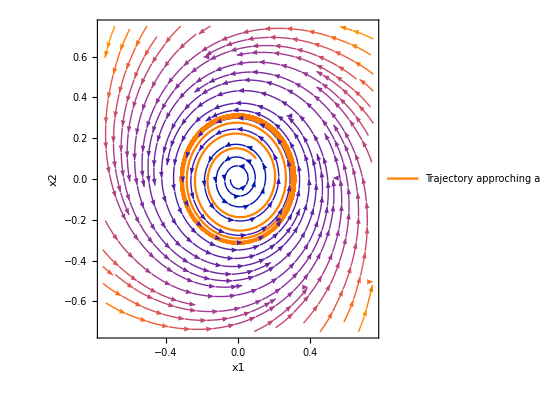

```mathematica
Clear["Global`*"]
X1[x1_, x2_] := 1/10*x1 - x2^3 - x1*x2^2 - x1^2*x2 - x2 - x1^3;
X2[x1_, x2_] := x1 + 1/10*x2 + x1*x2^2 + x1^3 - x2^3 - x1^2*x2;
streamPlot =StreamPlot[{X1[x1, x2], X2[x1, x2]}, {x1, -.75, .75}, {x2, -.75, .75},FrameLabel->{"x1","x2"}];
X1T := x1'[t] == 1/10*x1[t] - x2[t]^3 - x1[t]*x2[t]^2 - x1[t]^2*x2[t] - x2[t] - x1[t]^3;
X2T := x2'[t] ==x1[t] + 1/10*x2[t] + x1[t]*x2[t]^2 + x1[t]^3 - x2[t]^3 - x1[t]^2*x2[t];
limitCycle=NDSolve[{X1T,X2T,x1[0]==x2[0]== 0.1},{x1, x2},{t,0,100}];
trajectory=ParametricPlot[Evaluate[{x1[t],x2[t]}/. {limitCycle},{t,0,100},PlotStyle->{Orange}],  PlotLegends->{"Trajectory approching a limit cycle"}];
Show[streamPlot,trajectory]
```

```mathematica
Clear["Global`*"]
dr[r_] := μ*r - r^3;
dθ[r_] := ω + ν*r^2;
X1[x1_, x2_] := 1/10*x1 - x2^3 - x1*x2^2 - x1^2*x2 - x2 - x1^3;
X2[x1_, x2_] := x1 + 1/10*x2 + x1*x2^2 + x1^3 - x2^3 - x1^2*x2;
(*  r^2 = x^2 + y^2
2rr' = 2xx' + 2yy'
x' = (rr' - yy')/x. (1)
θ = arctan(y/x)
θ' = (xy' - yx')/r^2
-> x' = xy' - r^2θ'. (2)
Put (1) equal to (2) and solve for x'.
-> x' = x/r*r' - yθ'.
Similarly for y we get:
y' = y/r*r' - xθ'. *)
dx1[x1_, x2_] := x1/Sqrt[x1^2+x2^2] *dr[Sqrt[x1^2+x2^2]]- x2*dθ[Sqrt[x1^2+x2^2]];
dx2[x1_, x2_] := x2/Sqrt[x1^2+x2^2]*dr[Sqrt[x1^2+x2^2]] - x1*dθ[Sqrt[x1^2+x2^2]];
Simplify[dx1[x1, x2]]
X1[x1, x2]
(* From looking at the equations we get: μ = 1/10, ω = 1 and ν = 1 *)
```

-x1^3+x1 (-x2^2+μ)-x1^2 x2 ν-x2 (x2^2 ν+ω)

x1/10-x1^3-x2-x1^2 x2-x1 x2^2-x2^3

M21 (-1-x1^2-2 x1 x2-3 x2^2)+M11 (1/10-3 x1^2-2 x1 x2-x2^2)

M22 (-1-x1^2-2 x1 x2-3 x2^2)+M12 (1/10-3 x1^2-2 x1 x2-x2^2)

M21 (1/10-x1^2+2 x1 x2-3 x2^2)+M11 (1+3 x1^2-2 x1 x2+x2^2)

M22 (1/10-x1^2+2 x1 x2-3 x2^2)+M12 (1+3 x1^2-2 x1 x2+x2^2)

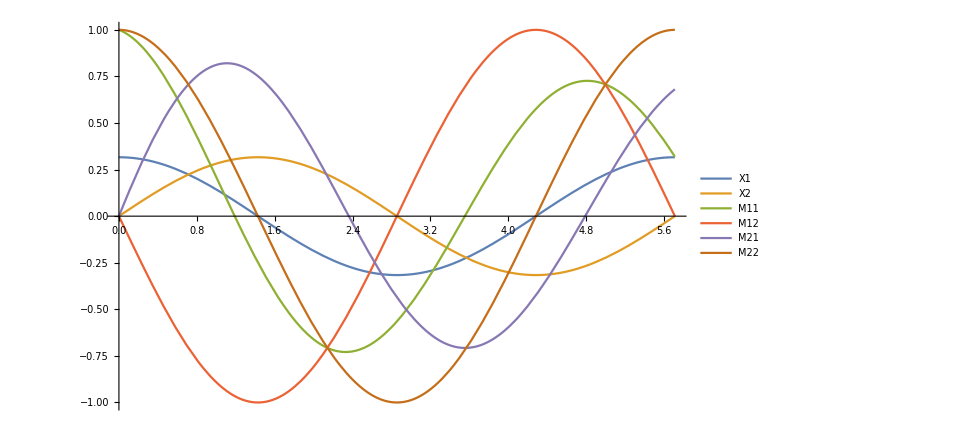

{{0.319053,2.12317×10^-8,0.680947,1.}}

{5.78753×10^-9,-0.2}

```mathematica
Clear["Global`*"]
μ= 1/10; ω = 1 ;ν = 1;T = (2 π)/(μ ν+ω);
F1[x1_, x2_] := 1/10*x1 - x2^3 - x1*x2^2 - x1^2*x2 - x2 - x1^3;
F2[x1_, x2_] := x1 + 1/10*x2 + x1*x2^2 + x1^3 - x2^3 - x1^2*x2;
J[x1_, x2_] := {{D[F1[x1,x2],x1],D[F1[x1,x2],x2]}, {D[F2[x1,x2],x1],D[F2[x1,x2],x2]}};
M11[x1, x2]=J[x1, x2][[1]][[1]]M11 + J[x1, x2][[1]][[2]]M21
M12[x1, x2]=J[x1, x2][[1]][[1]]M12 + J[x1, x2][[1]][[2]]M22
M21[x1, x2]=J[x1, x2][[2]][[1]]M11 + J[x1, x2][[2]][[2]]M21
M22[x1, x2]=J[x1, x2][[2]][[1]]M12 + J[x1, x2][[2]][[2]]M22
s=NDSolve[{x1'[t]==1/10*x1[t] - x2[t]^3 - x1[t]*x2[t]^2 - x1[t]^2*x2[t] - x2[t] - x1[t]^3,   x2'[t]== x1[t] + 1/10*x2[t] + x1[t]*x2[t]^2 + x1[t]^3 - x2[t]^3 - x1[t]^2*x2[t], 
m11'[t] == m21[t]*(-1-x1[t]^2-2 x1[t] x2[t]-3 x2[t]^2)+m11[t]*(1/10-3 x1[t]^2-2 x1[t] x2[t]-x2[t]^2),
m12'[t] == m22[t]*(-1-x1[t]^2-2 x1[t] x2[t]-3 x2[t]^2)+m12[t]*(1/10-3 x1[t]^2-2 x1[t] x2[t]-x2[t]^2),
m21'[t] == m21[t]*(1/10-x1[t]^2+2 x1[t] x2[t]-3 x2[t]^2)+m11[t]*(1+3 x1[t]^2-2 x1[t] x2[t]+x2[t]^2),
m22'[t] == m22[t]*(1/10-x1[t]^2+2 x1[t] x2[t]-3 x2[t]^2)+m12[t]*(1+3 x1[t]^2-2 x1[t] x2[t]+x2[t]^2),
 x1[0]== Sqrt[μ], x2[0]==0, m11[0]==m22[0]==1,m12[0]==m21[0]==0},{x1, x2, m11, m12, m21, m22},{t,0,T}];
Plot[{Evaluate[x1[t]/. s], Evaluate[x2[t]/. s],Evaluate[m11[t]/. s], Evaluate[m12[t]/. s],Evaluate[m21[t]/. s],Evaluate[m22[t]/. s]},{t,0,T}, PlotLegends->{"X1", "X2", "M11", "M12", "M21","M22"}]
M ={m11[T], m12[T],m21[T],m22[T]}/. s
λ = 1/T*Log[Eigenvalues[{{M[[1]][[1]],M[[1]][[2]]}, {M[[1]][[3]], M[[1]][[4]]}}]]
```

```mathematica
Clear["Global`*"]
μ= 1/10; ω = 1 ;ν = 1;T = (2 π)/(μ ν+ω);
r[r_] := μ*r - r^3;
θ[r_] := ω + ν*r^2;
Jp[r_] := {{D[r[r],r],D[r[r],θ]}, {D[θ[r], r],D[θ[r], θ]}};
Jp = Jp[r];
Mpolar[r_] := IdentityMatrix[2].MatrixExp[Jp];
Mpolar = Mpolar[r]
JG[x1_, x2_] := {{D[Sqrt[x1^2+x2^2],x1],D[Sqrt[x1^2+x2^2],x2]}, {D[ArcTan[x1,x2], x1],D[ArcTan[x1,x2], x2]}};
JG = JG[x1, x2]/. {x1-> r*Cos[θ], x2-> r*Sin[θ]}
JGinv[r_] := {{D[r*Cos[θ],r],D[r*Cos[θ],θ]}, {D[r*Sin[θ],r],D[r*Sin[θ],θ]}};
JGinv = JGinv[r]
Mcart = JGinv.Mpolar.JG /. {r-> Sqrt[μ], θ-> 0};
Mcart = Simplify[Mcart]
λ = 1/T*Log[Eigenvalues[Mpolar] /. r-> Sqrt[μ]]
λ = 1/T*Log[Eigenvalues[Mcart] /. r-> Sqrt[μ]]
```

{{ⅇ^(1/10-3 r^2),0},{(20 ⅇ^(-3 r^2) (-ⅇ^(1/10)+ⅇ^(3 r^2)) r)/(-1+30 r^2),1}}

{{(r Cos[θ])/(√(r^2 Cos[θ]^2+r^2 Sin[θ]^2)),(r Sin[θ])/(√(r^2 Cos[θ]^2+r^2 Sin[θ]^2))},{-(r Sin[θ])/(r^2 Cos[θ]^2+r^2 Sin[θ]^2),(r Cos[θ])/(r^2 Cos[θ]^2+r^2 Sin[θ]^2)}}

{{Cos[θ],-r Sin[θ]},{Sin[θ],r Cos[θ]}}

{{1/ⅇ^(1/5),0},{1-1/ⅇ^(1/5),1}}

{-11/(100 π),0}

{0,-11/(100 π)}